```mathematica
fθ=π If[Abs[ky]≤Abs[kx],Abs[kx],Abs[ky]];
fϕ=ArcTan[kx,ky];
(*Winding number that fixes the Euler class to χ= 2 mn*)
mn=1;2;
(*energy eigenvalues*)
ϵ1n=-1;
ϵ2n=-1;
ϵ3n=1.;
(*Bloch Hamiltonian in the basis of the Gell-Mann matrices*)
h0=1/3 (ϵ1+ϵ2+ϵ3)/.{ϵ1->ϵ1n,ϵ2->ϵ2n,ϵ3->ϵ3n};
h1=Cos[m fϕ] (-ϵ2+ϵ1 Cos[fθ]^2+ϵ3 Sin[fθ]^2) Sin[m fϕ]/.{m->mn}/.{ϵ1->ϵ1n,ϵ2->ϵ2n,ϵ3->ϵ3n};
h3=1/4 (ϵ1-2 ϵ2+ϵ3+(ϵ1-ϵ3) Cos[2 (fθ)]) Cos[2 fϕ m]/.{m->mn}/.{ϵ1->ϵ1n,ϵ2->ϵ2n,ϵ3->ϵ3n};h4=(-ϵ1+ϵ3) Cos[fθ] Sin[fθ]Cos[fϕ m]/.{m->mn}/.{ϵ1->ϵ1n,ϵ2->ϵ2n,ϵ3->ϵ3n};h6=(-ϵ1+ϵ3) Cos[fθ] Sin[fθ] Sin[fϕ m]/.{m->mn}/.{ϵ1->ϵ1n,ϵ2->ϵ2n,ϵ3->ϵ3n};h8=(-ϵ1+2 ϵ2-ϵ3+3 (ϵ1-ϵ3) Cos[2 fθ])/(4 √3)/.{ϵ1->ϵ1n,ϵ2->ϵ2n,ϵ3->ϵ3n};
(*Hamiltonian at Γ*)
h00=1/3 (ϵ1+ϵ2+ϵ3)/.{ϵ1->ϵ1n,ϵ2->ϵ2n,ϵ3->ϵ3n}/.{kx->0,ky->0};

h10=Cos[m 0] (-ϵ2+ϵ1 Cos[0]^2+ϵ3 Sin[0]^2) Sin[m 0]/.{m->mn}/.{ϵ1->ϵ1n,ϵ2->ϵ2n,ϵ3->ϵ3n}/.{kx->0,ky->0};
h30=1/4 (ϵ1-2 ϵ2+ϵ3+(ϵ1-ϵ3) Cos[2 (0)]) Cos[2 0 m]/.{m->mn}/.{ϵ1->ϵ1n,ϵ2->ϵ2n,ϵ3->ϵ3n}/.{kx->0,ky->0};h40=(-ϵ1+ϵ3) Cos[0] Sin[0]Cos[0 m]/.{m->mn}/.{ϵ1->ϵ1n,ϵ2->ϵ2n,ϵ3->ϵ3n}/.{kx->0,ky->0};h60=(-ϵ1+ϵ3) Cos[0] Sin[0] Sin[0 m]/.{m->mn}/.{ϵ1->ϵ1n,ϵ2->ϵ2n,ϵ3->ϵ3n}/.{kx->0,ky->0};h80=(-ϵ1+2 ϵ2-ϵ3+3 (ϵ1-ϵ3) Cos[2 0])/(4 √3)/.{ϵ1->ϵ1n,ϵ2->ϵ2n,ϵ3->ϵ3n}/.{kx->0,ky->0};
```

```mathematica
Quiet[
Nk=10;40;50;50;
K1=Table[i,{i,-1.,1.,1./Nk}];
K2=Table[i,{i,-1.,1.,1./Nk}];
NK1=Dimensions[K1][[1]];
NK2=Dimensions[K2][[1]];
h0n=Table[N[h0/.{kx->K1[[i]],ky->K2[[j]]}],{i,1,NK1},{j,1,NK2}];
h1n=Table[N[h1/.{kx->K1[[i]],ky->K2[[j]]}],{i,1,NK1},{j,1,NK2}];
h3n=Table[N[h3/.{kx->K1[[i]],ky->K2[[j]]}],{i,1,NK1},{j,1,NK2}];
h4n=Table[N[h4/.{kx->K1[[i]],ky->K2[[j]]}],{i,1,NK1},{j,1,NK2}];
h6n=Table[N[h6/.{kx->K1[[i]],ky->K2[[j]]}],{i,1,NK1},{j,1,NK2}];
h8n=Table[N[h8/.{kx->K1[[i]],ky->K2[[j]]}],{i,1,NK1},{j,1,NK2}];
h0n[[Nk+1,Nk+1]]=h00;
h1n[[Nk+1,Nk+1]]=h10;
h3n[[Nk+1,Nk+1]]=h30;
h4n[[Nk+1,Nk+1]]=h40;
h6n[[Nk+1,Nk+1]]=h60;
h8n[[Nk+1,Nk+1]]=h80;]
```

```mathematica
Nx=3;(*number of neighbors!*)
Ny=3;
coff=Norm[{Nx,Nx}];(Nx+Ny)/4+Norm[{Nx,Nx}]/2;
nx=Table[i,{i,-Nx,Nx}];
ny=Table[j,{j,-Ny,Ny}];
Nnx=Dimensions[nx][[1]];
Nny=Dimensions[ny][[1]];
t0=1/((NK1-1)(NK2-1))Table[(Sum[Exp[-I π {K1[[i]],K2[[j]]}.{nx[[ix]],ny[[iy]]}]h0n[[i,j]],{i,1,NK1-1},{j,1,NK2-1}]),{ix,1,Nnx},{iy,1,Nny}];
t1=1/((NK1-1)(NK2-1))Table[(Sum[Exp[-I π {K1[[i]],K2[[j]]}.{nx[[ix]],ny[[iy]]}]h1n[[i,j]],{i,1,NK1-1},{j,1,NK2-1}]),{ix,1,Nnx},{iy,1,Nny}];
t3=1/((NK1-1)(NK2-1))Table[(Sum[Exp[-I π {K1[[i]],K2[[j]]}.{nx[[ix]],ny[[iy]]}]h3n[[i,j]],{i,1,NK1-1},{j,1,NK2-1}]),{ix,1,Nnx},{iy,1,Nny}];
t4=1/((NK1-1)(NK2-1))Table[(Sum[Exp[-I π {K1[[i]],K2[[j]]}.{nx[[ix]],ny[[iy]]}]h4n[[i,j]],{i,1,NK1-1},{j,1,NK2-1}]),{ix,1,Nnx},{iy,1,Nny}];
t6=1/((NK1-1)(NK2-1))Table[(Sum[Exp[-I π {K1[[i]],K2[[j]]}.{nx[[ix]],ny[[iy]]}]h6n[[i,j]],{i,1,NK1-1},{j,1,NK2-1}]),{ix,1,Nnx},{iy,1,Nny}];
t8=1/((NK1-1)(NK2-1))Table[(Sum[Exp[-I π {K1[[i]],K2[[j]]}.{nx[[ix]],ny[[iy]]}]h8n[[i,j]],{i,1,NK1-1},{j,1,NK2-1}]),{ix,1,Nnx},{iy,1,Nny}];
h0I=Sum[If[Norm[{nx[[ix]],ny[[iy]]}]≤coff,Exp[I π {kx,ky}.{nx[[ix]],ny[[iy]]}] t0[[ix,iy]],0],{ix,1,Nnx},{iy,1,Nny}];
h1I=Sum[If[Norm[{nx[[ix]],ny[[iy]]}]≤coff,Exp[I π {kx,ky}.{nx[[ix]],ny[[iy]]}] t1[[ix,iy]],0],{ix,1,Nnx},{iy,1,Nny}];
h3I=Sum[If[Norm[{nx[[ix]],ny[[iy]]}]<=coff,Exp[I π {kx,ky}.{nx[[ix]],ny[[iy]]}] t3[[ix,iy]],0],{ix,1,Nnx},{iy,1,Nny}];
h4I=Sum[If[Norm[{nx[[ix]],ny[[iy]]}]<=coff,Exp[I π {kx,ky}.{nx[[ix]],ny[[iy]]}] t4[[ix,iy]],0],{ix,1,Nnx},{iy,1,Nny}];
h6I=Sum[If[Norm[{nx[[ix]],ny[[iy]]}]<=coff,Exp[I π {kx,ky}.{nx[[ix]],ny[[iy]]}] t6[[ix,iy]],0],{ix,1,Nnx},{iy,1,Nny}];
h8I=Sum[If[Norm[{nx[[ix]],ny[[iy]]}]<=coff,Exp[I π {kx,ky}.{nx[[ix]],ny[[iy]]}] t8[[ix,iy]],0],{ix,1,Nnx},{iy,1,Nny}];
```

```mathematica
Nk=40;
{Aa,Bb,Cc,Dd}={-1.,1.,-1,1.};
K1=Table[i ,{i,Aa,Bb,(Bb-Aa)/Nk}];
K2=Table[i,{i,Cc,Dd,(Dd-Cc)/Nk}];
GM0={{1,0,0},{0,1,0},{0,0,1}};
GM1={{0,1,0},{1,0,0},{0,0,0}};
GM2={{0,-I,0},{I,0,0},{0,0,0}};
GM3={{1,0,0},{0,-1,0},{0,0,0}};
GM4={{0,0,1},{0,0,0},{1,0,0}};
GM5={{0,0,-I},{0,0,0},{I,0,0}};
GM6={{0,0,0},{0,0,1},{0,1,0}};
GM7={{0,0,0},{0,0,-I},{0,I,0}};
GM8=1/Sqrt[3]{{1,0,0},{0,1,0},{0,0,-2}};
Hn={h0I,h1I,h3I,h4I,h6I,h8I}.{GM0,GM1,GM3,GM4,GM6,GM8};
En=Table[Sort[Re[Eigenvalues[N[Hn/.{kx->K1[[i]],ky->K2[[j]]}]]]],{i,1,Dimensions[K1][[1]]},{j,1,Dimensions[K2][[1]]}];
ListPlot3D[Table[Transpose[En[[;;,;;,i]]],{i,1,3}],InterpolationOrder->1,AxesLabel->{"k_x","k_y","E"},ImageSize->500,DataRange->{{Aa,Bb},{Cc,Dd}},PlotStyle->{Opacity[0.8]}]
```

-Graphics3D-

```mathematica
WILSON LOOP
```

```mathematica
Nk=50;
Nk2=100;
BNbr=2;

Banda=1;1;3;
Bandb=2;2;4;

GM0={{1,0,0},{0,1,0},{0,0,1}};
GM1={{0,1,0},{1,0,0},{0,0,0}};
GM2={{0,-I,0},{I,0,0},{0,0,0}};
GM3={{1,0,0},{0,-1,0},{0,0,0}};
GM4={{0,0,1},{0,0,0},{1,0,0}};
GM5={{0,0,-I},{0,0,0},{I,0,0}};
GM6={{0,0,0},{0,0,1},{0,1,0}};
GM7={{0,0,0},{0,0,-I},{0,I,0}};
GM8=1/Sqrt[3]{{1,0,0},{0,1,0},{0,0,-2}};
(*Hw={h0,h1I,h3I,h4I,h6I,h8I}.{GM0,GM1,GM3,GM4,GM6,GM8};*)
(*DiagonalMatrix[{δ,-δ,0.}]/.{m->2.5,δ->0.1};HFn;*)

kx0=0.;
ky0=0.;
kdA=-1.;
kdB=1.;1.;
kd=Table[ν,{ν,kdA,kdB,(kdB-kdA)/Nk2}];
Dnu=Dimensions[kd][[1]];

BerryPhase=Table[0,{ν,1,Dnu}];
θ=Table[{0,0},{ν,1,Dnu}];
W=Table[IdentityMatrix[BNbr],{ν,1,Dnu}];

KD0=Table[{i,0},{i,-1,1,1/Nk}];

BP=Table[0,{ν,1,Dnu},{i,1,Dimensions[KD0][[1]]-1}];
WE=Table[{0,0},{ν,1,Dnu},{i,1,Dimensions[KD0][[1]]-1}];
SPEC=Table[{0,0,0,0},{ν,1,Dnu},{i,1,Dimensions[KD0][[1]]}];
UKeep=Table[0,{ν,1,Dnu},{i,1,Dimensions[KD0][[1]]},{n,1,2BNbr},{m,1,BNbr}];

Do[

KD=Table[{i,0},{i,-1.,1.,1/Nk}];

P1=Table[IdentityMatrix[BNbr],{i,1,Dimensions[KD][[1]]-1}];

EigV=Table[Transpose[Sort[Transpose[Eigensystem[Hn/.{kx->kx0+KD[[i,1]],ky->ky0+KD[[i,2]]+kd[[ν]]}]]]],{i,1,Dimensions[KD][[1]]}];
SPEC[[ν]]=EigV[[;;,1]];
U=Table[Transpose[EigV[[i,2]][[{Banda,Bandb}]]],{i,1,Dimensions[KD][[1]]}];
UKeep[[ν]]=U;

P1=Table[ConjugateTranspose[U[[i+1]]].U[[i]],{i,1,Dimensions[KD][[1]]-1}];

ProdB=IdentityMatrix[BNbr];
Do[ProdB=P1[[i]].ProdB,{i,1,Dimensions[KD][[1]]-2}];
ProdB=ConjugateTranspose[U[[1]]].U[[Dimensions[KD][[1]]-1]].ProdB;(*TG[G1].*)

W[[ν]]=ProdB;
θ[[ν]]=Im[Log[Eigenvalues[ProdB]]]/π;
BerryPhase[[ν]]=Arg[Det[ProdB]]/π,{ν,1,Dnu}];
```

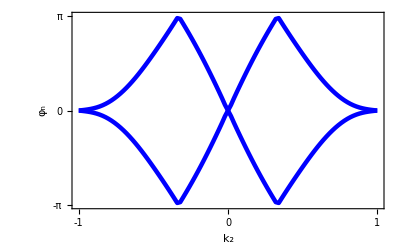

```mathematica
θo=Table[Sort[θ[[i,;;]]],{i,1,Dimensions[θ][[1]]}];
ListPlot[Table[θo[[1;;,i]],{i,1,BNbr}],Joined->True, PlotRange->{{-1.005,1.005},{-1.0,1.0}},Frame->True,FrameLabel->{"k_2","φ_n"},FrameTicks->{{{{-1,"-π"},0,{1,"π"}},None},{{-1,0,1},None}},DataRange->{-1,1},PlotStyle->{Directive[{Thickness[0.008],Blue}]},LabelStyle->{Directive[20],Black}]
```